```mathematica
v=5,H=10,g=10
```

```mathematica
Manipulate[ParametricPlot[{v t Sin[a],10+v t Cos[a]-5 t^2},{t,0,5},PlotRange->{0,15}],{{a,Pi/4},0,Pi/2},{{v,6},3,10}]
```

```mathematica
Eliminate[v t Sin[a]==x&&H+v t Cos[a]-1/2 g t^2==y,t]
```

g x^2-2 v^2 x Cos[a] Sin[a]+2 v^2 y Sin[a]^2==2 H v^2 Sin[a]^2

```mathematica
Solve[g x^2-2 v^2 x Cos[a] Sin[a]+2 v^2 y Sin[a]^2==2 H v^2 Sin[a]^2,y]
Simplify[%]
```

{{y→(2 H v^2+2 v^2 x Cot[a]-g x^2 Csc[a]^2)/(2 v^2)}}

{{y→H+x Cot[a]-(g x^2 Csc[a]^2)/(2 v^2)}}

```mathematica
Solve[H+x Cot[a]-(g x^2 Csc[a]^2)/(2 v^2)==0,x]
```

{{x→-(v^2 (-Cot[a]-√(Cot[a]^2+(2 g H Csc[a]^2)/v^2)) Sin[a]^2)/g},{x→-(v^2 (-Cot[a]+√(Cot[a]^2+(2 g H Csc[a]^2)/v^2)) Sin[a]^2)/g}}

```mathematica
It is too complex


func={5 t Sin[a],10+5 t Cos[a]-5 t^2}
tab=Table[func,{a,0,2Pi,Pi/36}]
```

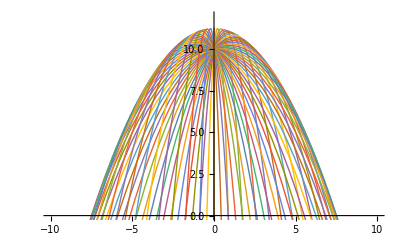

```mathematica
ParametricPlot[tab,{t,0,5},PlotRange->{{-10,10},{0,12}},PlotStyle->Directive[Thin]]
```

{5 t Sin[a],10-5 t^2+5 t Cos[a]}

{{0,10+5 t-5 t^2},{5 t Sin[π/36],10-5 t^2+5 t Cos[π/36]},{5 t Sin[π/18],10-5 t^2+5 t Cos[π/18]},{(5 (-1+√3) t)/(2 √2),10+(5 (1+√3) t)/(2 √2)-5 t^2},{5 t Sin[π/9],10-5 t^2+5 t Cos[π/9]},{5 t Sin[(5 π)/36],10-5 t^2+5 t Cos[(5 π)/36]},{(5 t)/2,10+(5 √3 t)/2-5 t^2},{5 t Sin[(7 π)/36],10-5 t^2+5 t Cos[(7 π)/36]},{5 t Sin[(2 π)/9],10-5 t^2+5 t Cos[(2 π)/9]},{(5 t)/(√2),10+(5 t)/(√2)-5 t^2},{5 t Cos[(2 π)/9],10-5 t^2+5 t Sin[(2 π)/9]},{5 t Cos[(7 π)/36],10-5 t^2+5 t Sin[(7 π)/36]},{(5 √3 t)/2,10+(5 t)/2-5 t^2},{5 t Cos[(5 π)/36],10-5 t^2+5 t Sin[(5 π)/36]},{5 t Cos[π/9],10-5 t^2+5 t Sin[π/9]},{(5 (1+√3) t)/(2 √2),10+(5 (-1+√3) t)/(2 √2)-5 t^2},{5 t Cos[π/18],10-5 t^2+5 t Sin[π/18]},{5 t Cos[π/36],10-5 t^2+5 t Sin[π/36]},{5 t,10-5 t^2},{5 t Cos[π/36],10-5 t^2-5 t Sin[π/36]},{5 t Cos[π/18],10-5 t^2-5 t Sin[π/18]},{(5 (1+√3) t)/(2 √2),10-(5 (-1+√3) t)/(2 √2)-5 t^2},{5 t Cos[π/9],10-5 t^2-5 t Sin[π/9]},{5 t Cos[(5 π)/36],10-5 t^2-5 t Sin[(5 π)/36]},{(5 √3 t)/2,10-(5 t)/2-5 t^2},{5 t Cos[(7 π)/36],10-5 t^2-5 t Sin[(7 π)/36]},{5 t Cos[(2 π)/9],10-5 t^2-5 t Sin[(2 π)/9]},{(5 t)/(√2),10-(5 t)/(√2)-5 t^2},{5 t Sin[(2 π)/9],10-5 t^2-5 t Cos[(2 π)/9]},{5 t Sin[(7 π)/36],10-5 t^2-5 t Cos[(7 π)/36]},{(5 t)/2,10-(5 √3 t)/2-5 t^2},{5 t Sin[(5 π)/36],10-5 t^2-5 t Cos[(5 π)/36]},{5 t Sin[π/9],10-5 t^2-5 t Cos[π/9]},{(5 (-1+√3) t)/(2 √2),10-(5 (1+√3) t)/(2 √2)-5 t^2},{5 t Sin[π/18],10-5 t^2-5 t Cos[π/18]},{5 t Sin[π/36],10-5 t^2-5 t Cos[π/36]},{0,10-5 t-5 t^2},{-5 t Sin[π/36],10-5 t^2-5 t Cos[π/36]},{-5 t Sin[π/18],10-5 t^2-5 t Cos[π/18]},{-(5 (-1+√3) t)/(2 √2),10-(5 (1+√3) t)/(2 √2)-5 t^2},{-5 t Sin[π/9],10-5 t^2-5 t Cos[π/9]},{-5 t Sin[(5 π)/36],10-5 t^2-5 t Cos[(5 π)/36]},{-(5 t)/2,10-(5 √3 t)/2-5 t^2},{-5 t Sin[(7 π)/36],10-5 t^2-5 t Cos[(7 π)/36]},{-5 t Sin[(2 π)/9],10-5 t^2-5 t Cos[(2 π)/9]},{-(5 t)/(√2),10-(5 t)/(√2)-5 t^2},{-5 t Cos[(2 π)/9],10-5 t^2-5 t Sin[(2 π)/9]},{-5 t Cos[(7 π)/36],10-5 t^2-5 t Sin[(7 π)/36]},{-(5 √3 t)/2,10-(5 t)/2-5 t^2},{-5 t Cos[(5 π)/36],10-5 t^2-5 t Sin[(5 π)/36]},{-5 t Cos[π/9],10-5 t^2-5 t Sin[π/9]},{-(5 (1+√3) t)/(2 √2),10-(5 (-1+√3) t)/(2 √2)-5 t^2},{-5 t Cos[π/18],10-5 t^2-5 t Sin[π/18]},{-5 t Cos[π/36],10-5 t^2-5 t Sin[π/36]},{-5 t,10-5 t^2},{-5 t Cos[π/36],10-5 t^2+5 t Sin[π/36]},{-5 t Cos[π/18],10-5 t^2+5 t Sin[π/18]},{-(5 (1+√3) t)/(2 √2),10+(5 (-1+√3) t)/(2 √2)-5 t^2},{-5 t Cos[π/9],10-5 t^2+5 t Sin[π/9]},{-5 t Cos[(5 π)/36],10-5 t^2+5 t Sin[(5 π)/36]},{-(5 √3 t)/2,10+(5 t)/2-5 t^2},{-5 t Cos[(7 π)/36],10-5 t^2+5 t Sin[(7 π)/36]},{-5 t Cos[(2 π)/9],10-5 t^2+5 t Sin[(2 π)/9]},{-(5 t)/(√2),10+(5 t)/(√2)-5 t^2},{-5 t Sin[(2 π)/9],10-5 t^2+5 t Cos[(2 π)/9]},{-5 t Sin[(7 π)/36],10-5 t^2+5 t Cos[(7 π)/36]},{-(5 t)/2,10+(5 √3 t)/2-5 t^2},{-5 t Sin[(5 π)/36],10-5 t^2+5 t Cos[(5 π)/36]},{-5 t Sin[π/9],10-5 t^2+5 t Cos[π/9]},{-(5 (-1+√3) t)/(2 √2),10+(5 (1+√3) t)/(2 √2)-5 t^2},{-5 t Sin[π/18],10-5 t^2+5 t Cos[π/18]},{-5 t Sin[π/36],10-5 t^2+5 t Cos[π/36]},{0,10+5 t-5 t^2}}

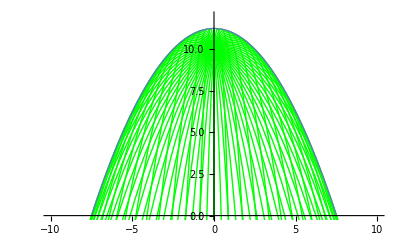

```mathematica
func={5 t Sin[a],10+5 t Cos[a]-5 t^2}
tab=Table[func,{a,0,2Pi,Pi/36}]
Show[ParametricPlot[tab,{t,0,5},PlotRange->{{-10,10},{0,12}},PlotStyle->Directive[Thin,Green]],Plot[1/20 (225-4 x^2),{x,-10,10},PlotRange->{{-10,10},{0,12}},PlotStyle->Directive[Thick]]]
```

```mathematica
D[H+x Cot[a]-(g x^2 Csc[a]^2)/(2 v^2)-y,a]
```

-x Csc[a]^2+(g x^2 Cot[a] Csc[a]^2)/v^2

```mathematica
Eliminate[-x Csc[a]^2+(g x^2 Cot[a] Csc[a]^2)/v^2==0&&H+x Cot[a]-(g x^2 Csc[a]^2)/(2 v^2)-y==0,a]
```

Eliminate::ifun: Eliminate 正在使用反函数，因此可能无法找到某些解；请使用 Reduce 来获取完整的解信息.

2 g H x==x (-v^2+(g^2 x^2)/v^2+2 g y)&&4 g H^2+H (2 v^2-8 g y)==-g x^2+(g^3 x^4)/v^4+2 v^2 y-4 g y^2&&v≠0

```mathematica
Solve[2 g H x==x (-v^2+(g^2 x^2)/v^2+2 g y),y]
```

```mathematica
{{y->(2 g H v^2+v^4-g^2 x^2)/(2 g v^2)}}
```

```mathematica
Solve[(2 g H v^2+v^4-g^2 x^2)/(2 g v^2)==0,x]
```

{{x→-(v √(2 g H+v^2))/g},{x→(v √(2 g H+v^2))/g}}

```mathematica
max distance
```

```mathematica
Solve[2 10 10 x-x (-5^2+(10^2 x^2)/5^2+2 10 y)==0,y]
```

{{y→1/20 (225-4 x^2)}}

```mathematica
some examples
```

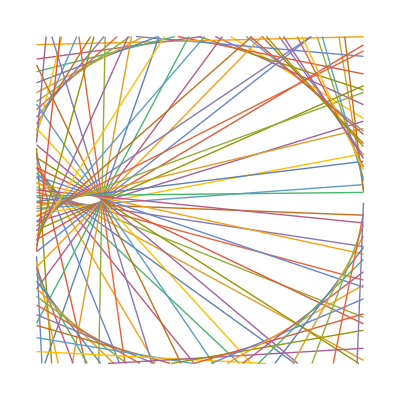

```mathematica
fuc0=FromPolarCoordinates[{4 Cos[θ/3]^3,θ}];
fuc1=FullSimplify[Last[fuc0]+D[Last[fuc0],θ]*(x-First[fuc0])/D[First[fuc0],θ]];
fuc2=Simplify[N[Table[fuc1,{θ,0,10,0.1}]]];
Plot[fuc2,{x,-1,4},PlotRange->3,PlotStyle->Directive[Thin],AspectRatio->1,Axes->False]
```